```mathematica
n=50;
```

```mathematica
(*k=AdjacencyMatrix[RandomGraph[{n,100}]];
AdjacencyGraph[k]*)
```

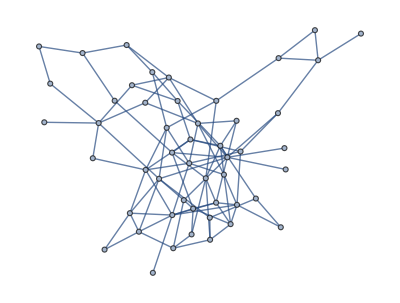
```mathematica
k1=-Graphics-;
```

```mathematica
k=AdjacencyMatrix[k1]
```

SparseArray[<200>, {50, 50}]

```mathematica
data={0.12208772056228683,0.47111213694397824,0.6181369384554125,0.06386630929439865,0.9777423254909376,-0.040214171772268346,-0.12465762556578931,0.37527822396278737,-0.08889863184230143,0.1534880407352289,0.3339108861931336,1.1872758902655196,-0.5723058518055973,0.3430414251428931,0.11854784848831793,-0.5369506038568154,-0.313195520766485,0.31085469354231204,-0.3693449712164738,0.5362889303756709,-0.4188655022668244,0.25201748992329515,0.01779154876834029,-0.04448268418953808,0.625288980425773,0.4363417695632045,0.8820893588464183,-0.3101303505785124,0.13879671784635292,0.06373931996807318,0.6277277704741051,-0.03668100330630939,-0.27158489623701987,-0.26783808709942075,0.53035076593487,0.4132219351687797,-0.09079590673546571,0.28232164445416963,-0.5469947123595892,-0.13774221455398067,0.1967718809399225,-0.40748740850381737,0.7160105008911652,-0.2822641922290987,0.778129754898415,-0.22362477170663966,0.27701502069766104,-0.15463265667126916,0.29013630381527966,-0.145800885953215};
```

```mathematica
m=3;
(*data=RandomVariate[VonMisesDistribution[0,5],n];*)
cmsol=Solve[1+a Sum[(m+1-mm)Cos[(2mm Pi)/(m+1)],{mm,1,m}]==0,a];
cmkoef=a/.cmsol[[1]];
eqns=Table[{Subscript[∅,i]'[t]==6-1.5/n Sum[k[[i]][[j]](cmkoef Sum[mm(m+1-mm)Sin[mm(Subscript[∅,j][t]-Subscript[∅,i][t])],{mm,1,m}]),{j,1,n}],Subscript[∅,i][0]==data[[i]]},{i,1,n}];
vars=Table[Subscript[∅,i][t],{i,1,n}];
sol=NDSolve[eqns,vars,{t,0,10000}];
Do[Subscript[z,i][t_]:=Evaluate[Subscript[∅,i][t]/.sol],{i,1,n}];
Do[Subscript[zz,i][t_]:=Evaluate[ⅇ^(ⅈ×Subscript[∅,i][t]/.sol)],{i,1,n}];
data1[t_]:=Flatten[Table[Subscript[zz,i][t],{i,1,n}]];
tt=10000;
lista=Sort[Table[Mod[Subscript[z,i][tt],2Pi][[1]],{i,1,n}]];
lisboj[t_]:=Table[Mod[Subscript[z,i][t],2Pi][[1]],{i,1,n}];
SomeGraph=AdjacencyGraph[k];
Table[lista[[i]]-lista[[i+1]],{i,1,n-1}]
ukupfrust[t_]:=Sum[k[[i]][[j]](1+cmkoef Sum[(m+1-mm)Cos[mm(Subscript[z,j][t]-Subscript[z,i][t])],{mm,1,m}]),{i,1,n},{j,i+1,n}]
ukupfrust[5000]
data2=Flatten[Table[Mod[Subscript[z,i][tt],2Pi],{i,1,n}]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.,0.,0.,-1.5708,0.,0.,0.,0.,0.,0.}

{0.}

{2.72117,2.72117,4.29196,4.29196,4.29196,1.15037,2.72117,4.29196,1.15037,2.72117,1.15037,4.29196,2.72117,4.29196,1.15037,1.15037,1.15037,2.72117,5.86276,2.72117,1.15037,2.72117,2.72117,1.15037,1.15037,2.72117,2.72117,5.86276,1.15037,2.72117,4.29196,1.15037,1.15037,5.86276,4.29196,2.72117,5.86276,2.72117,5.86276,1.15037,1.15037,5.86276,2.72117,1.15037,4.29196,1.15037,2.72117,1.15037,1.15037,5.86276}

```mathematica
zvuk={2,2,3,3,3,1,2,3,1,2,1,3,2,3,1,1,1,2,4,2,1,2,2,1,1,2,2,4,1,2,3,1,1,4,3,2,4,2,4,1,1,4,2,1,3,1,2,1,1,4};
```

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

```mathematica
a=Table[findAllRoots[Sin[(Subscript[z,i][t])/2],{t,0,40}],{i,1,n}];
```

```mathematica
Sound[Flatten[Table[Table[If[Round[a[[i]][[j]],0.05]==t,If[zvuk[[i]]==1,SoundNote["G",{t,t+0.1},"Harp"],If[zvuk[[i]]==2,SoundNote["B",{t,t+0.1},"Harp"],If[zvuk[[i]]==3,SoundNote["D",{t,t+0.1},"Harp"],SoundNote["F",{t,t+0.1},"Harp"]]]],SoundNote[None,{t,t+0.1}]],{i,1,n},{j,1,Length[a[[i]]]}],{t,0,40,0.05}]],{0,106.8}]
```

```mathematica
Export["sim6_harp.mp3",%29]
```

sim6_harp.mp3

```mathematica
Export["SM6.mid",%29]
```

SM6.mid

```mathematica
granica=40;
```

```mathematica
video[t_]:=Grid[{{AdjacencyGraph[k,EdgeStyle->Directive[Gray,Thickness[0.0035]],VertexStyle->Table[i->If[MemberQ[Round[a[[i]],0.1],t],White,Black],{i,1,n}],VertexSize->0.6,ImageSize->700],Show[{Plot[ukupfrust[tt],{tt,0,t+0.0000000001},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},PlotStyle->Directive[If[Chop[ukupfrust[10000]][[1]]==0,Red,Blue],Thickness[0.01]]]},AxesOrigin->{0,0},PlotRange->{{0,granica},{0,ukupfrust[0][[1]]}},ImageSize->600,Frame->True,FrameStyle->Directive[Black,25]]}},Spacings->0]
```

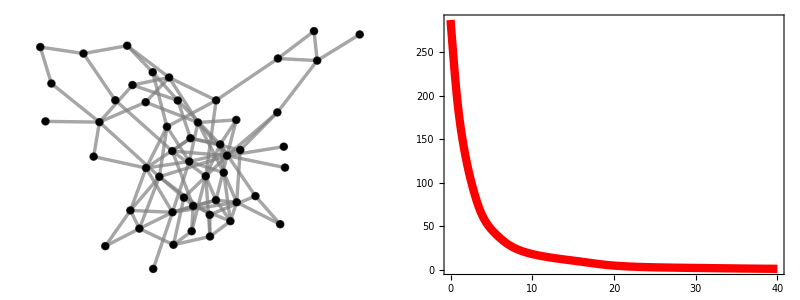

```mathematica
video[40]
```

```mathematica
simulaci2=Flatten[Table[Table[video[t],{i,1,2}],{t,0,40,0.05}]];
```

```mathematica
Export["SM6.AVI",simulaci2]
```